```mathematica
gpu=Import[NotebookDirectory[]<>"4890.csv","CSV"];
cpu=Import[NotebookDirectory[]<>"Corei7.csv","CSV"];
quadcpu=Import[NotebookDirectory[]<>"Core2Quad.csv","CSV"];
```

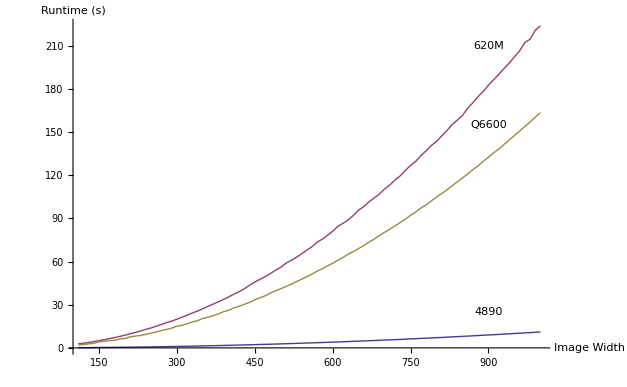

```mathematica
runtimePlot=Show[ListLinePlot[{gpu,cpu,quadcpu},PlotStyle->Thick,PlotRange->All,AxesOrigin->{100,0},AxesLabel->{"Image Width","Runtime (s)"}],Graphics[{
Text["Q6600",{900,155}],
Text["4890",{900,25}],
Text["620M",{900,210}]
}]]
```

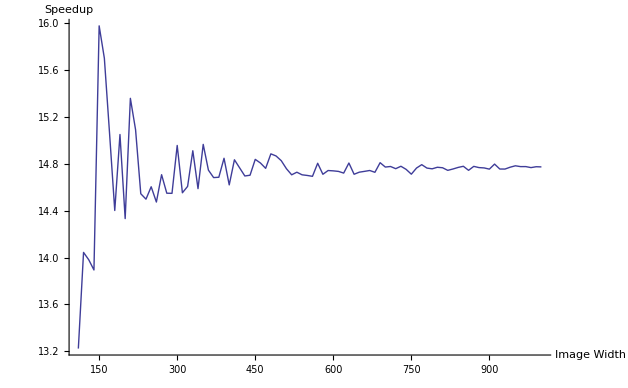

```mathematica
Speedup[a_,b_]:={a[[1]],b[[2]]/a[[2]]};
speedups=MapThread[Speedup,{gpu,quadcpu}];
speedupPlot=ListLinePlot[speedups,PlotStyle->Thick,PlotRange->All,AxesOrigin->{100,13},AxesLabel->{"Image Width","Speedup"}]
```

```mathematica
strongScaling:=Import[NotebookDirectory[]<>"strong.csv","CSV"];
```

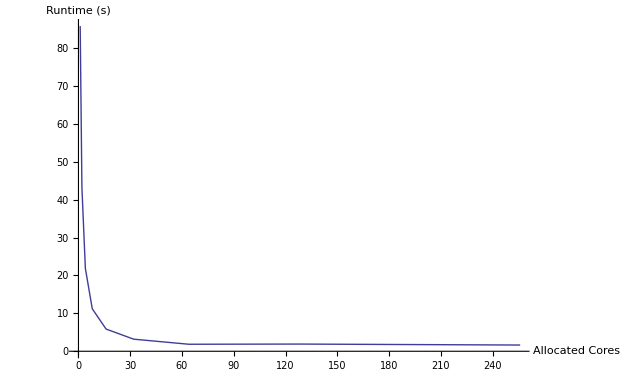

```mathematica
strongPlotOne=ListLinePlot[strongScaling,PlotStyle->Thick,AxesLabel->{"Allocated Cores","Runtime (s)"}]
```

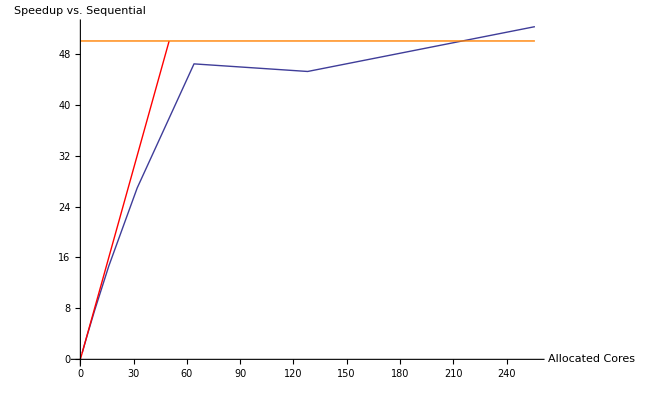

```mathematica
strongSpeedup={#[[1]],Last[First[strongScaling]]/#[[2]]}&/@strongScaling;
strongPlotTwo=Show[{ListLinePlot[strongSpeedup,PlotStyle->Thick,AxesLabel->{"Allocated Cores","Speedup vs. Sequential"}],Plot[x,{x,0,50},PlotStyle->{Red}],Plot[50,{x,0,256},PlotStyle->{Orange}]}]
```

```mathematica
Export["speedupPlot.pdf",speedupPlot]
```

speedupPlot.pdf